# Proporciones de estados y cambios

Compara varias evoluciones binarias que ocupan el mismo espacio y duran los mismos pasos. Se grafican dos proporciones respecto al total de celdas, con el paso en el eje x y la proporción en el eje y:

Unos en cada paso, de 0 al máximo observado.

Nacimientos (0 → 1), muertes (1 → 0) y quietos (sin cambio) en la transición del paso t − 1 al paso t, de 0 a 1. Las tres suman 1.

Cada evolución es una línea delgada y la línea gruesa es el promedio de todas.

## Archivos

Rutas relativas a la carpeta del notebook. Todas las evoluciones deben tener las mismas dimensiones.

```mathematica
SetDirectory[NotebookDirectory[]];
archivos=FileNames["*.mat","/home/rediax/Documents/ESCOM/Trabajo-Terminal/Simulator/training/NCA/B3S23_NR/1_01111111/best_evos"];
```

```mathematica
leerEvolucion[archivo_String]:=First[Import[archivo,"MAT"]];
evoluciones=leerEvolucion /@ archivos;
{Length[evoluciones],Union[Dimensions /@ evoluciones]}
```

{10,{{101,69,69}}}

## Medidas

```mathematica
celdas[evo_]:=Times @@ Rest[Dimensions[evo]];
proporciones[evo_]:=<|"Unos"->N[Total[evo,{2,3}]/celdas[evo]]|>;
cambios[evo_]:=With[{d=Differences[evo],n=N[celdas[evo]]},
	<|"Nacimientos"->Total[Clip[d,{0,1}],{2,3}]/n,
	  "Muertes"->Total[Clip[-d,{0,1}],{2,3}]/n,
	  "Quietos"->Total[1-Abs[d],{2,3}]/n|>];
datosProporciones=proporciones /@ evoluciones;
datosCambios=cambios /@ evoluciones;
```

## Gráficas

maximo es el límite superior del eje y (1 por defecto); las marcas del eje y las líneas guía usan las mismas divisiones. Con una sola medida no se agrega leyenda; el título la nombra.

```mathematica
colores=<|
	"Unos"->RGBColor["#2a78d6"],
	"Nacimientos"->RGBColor["#2a78d6"],"Muertes"->RGBColor["#eb6834"],"Quietos"->RGBColor["#1baf7a"]|>;
graficar[datos_List,pasos_List,titulo_String,maximo_ : 1]:=Module[{medidas=Keys[First[datos]],divisiones=FindDivisions[{0,maximo},6],grafica},
	grafica=Show[
		ListLinePlot[Flatten[Table[Transpose[{pasos,d[m]}],{m,medidas},{d,datos}],1],
			PlotStyle->Flatten[Table[ConstantArray[Directive[colores[m],Opacity[0.3],AbsoluteThickness[1]],Length[datos]],{m,medidas}],1]],
		ListLinePlot[Table[Transpose[{pasos,Mean[#[m] & /@ datos]}],{m,medidas}],
			PlotStyle->(Directive[colores[#],AbsoluteThickness[2]] & /@ medidas)],
		PlotRange->{{Min[pasos],Max[pasos]},{0,maximo}},Frame->True,Axes->False,
		FrameTicks->{{{#,NumberForm[N[#],{2,1}]} & /@ divisiones,None},{Automatic,None}},
		FrameLabel->{"Paso","Proporción"},PlotLabel->titulo,
		GridLines->{None,divisiones},GridLinesStyle->Directive[GrayLevel[0.85]],
		FrameStyle->GrayLevel[0.4],FrameTicksStyle->Directive[Black,11],LabelStyle->Directive[Black,12],
		ImageSize->400,AspectRatio->3/4];
	If[Length[medidas]==1,grafica,
		Legended[grafica,LineLegend[Values[KeyTake[colores,medidas]],medidas,LegendMarkerSize->{20,10}]]]];
pasos=Length[First[evoluciones]];
```

{{0.498005,0.331653,0.302247,0.287125,0.26528,0.245327,0.221382,0.21088,0.187776,0.172653,0.152279,0.130855,0.113212,0.10355,0.094938,0.0829658,0.0726738,0.063222,0.0581811,0.0520899,0.0470489,0.0415879,0.0378072,0.0340265,0.0298257,0.0281453,0.0270951,0.026255,0.0247847,0.0245747,0.0239445,0.0226843,0.0218442,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341,0.0216341}}

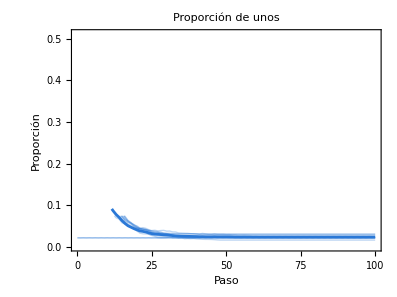

```mathematica
graficaProporciones=graficar[datosProporciones,Range[0,pasos-1],"Proporción de unos",Max[Values /@ datosProporciones]]
```

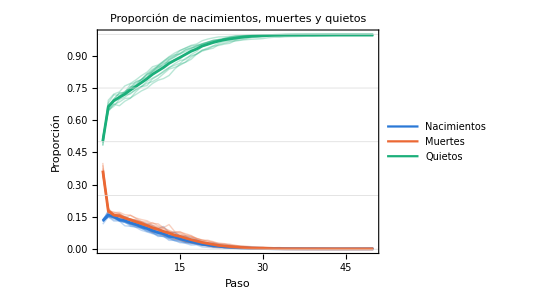

```mathematica
graficaCambios=graficar[datosCambios,Range[1,pasos-1],"Proporción de nacimientos, muertes y quietos"]
```

## Exportar

```mathematica
Export["../../../Documentation/img/b3s23_reduction_1s.png",graficaProporciones,ImageResolution->200];
Export["../../../Documentation/img/b3s23_reduction_changes.png",graficaCambios,ImageResolution->200];
```